# Ph 6 - Experiment 7 (The Kelvin Absolute Voltmeter)

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v10.x, Version 1.95, 1/2016

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/ybadal/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph 6/Lab 2/Kelvin.dat

File comment header:

Mass (mg) Voltage (V)

LoadFile::sorted: Data sorted in increasing x order.

Read 30 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

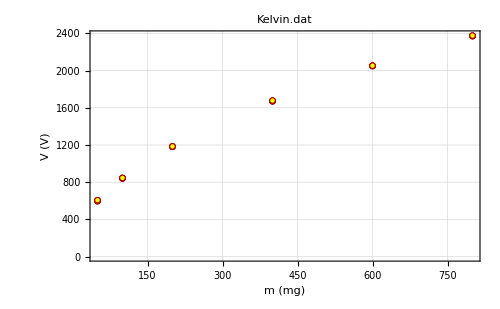

```mathematica
LinearDataPlot[FrameLabel->{"m (mg)","V (V)"}]
```

```mathematica
(* Converting into V/kg *)
```

```mathematica
xnew[ x_, y_ ] := x*10^-6
ynew[ x_, y_ ] := y
DataTransform[]
(* Use Undo[] if you don't like the results. *)
```

All 30 points transformed.

```mathematica
(* Squaring voltage values to obtain expected linear relationship *)
xnew[ x_, y_ ] := x 
ynew[ x_, y_ ] := y^2 
DataTransform[]
(* Use Undo[] if you don't like the results. *)
```

All 30 points transformed.

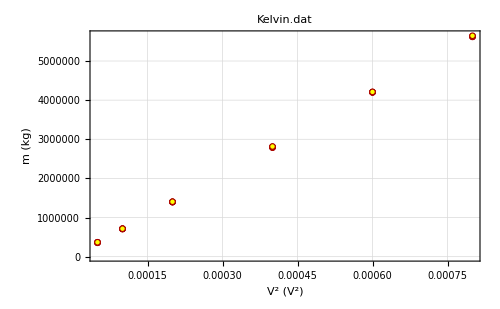

```mathematica
LinearDataPlot[FrameLabel->{"V^2 (V^2)","m (kg)"}]
```

## Fitting the V^2 against m data against a linear model

```mathematica
LinearFit[]
```

n = 30

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
3775.75 | b= 
7.01542×10^9 | 
σ_a= 
3516.48 | σ_b= 
7.82246×10^6 | Std. deviation= 
11628.6

Fit of (x,y±σ_y)

a= 
6941.72 | b= 
6.99929×10^9 | 
σ_a= 
1446.83 | σ_b= 
4.22734×10^6 | χ^2/(n-2)= 
2.828

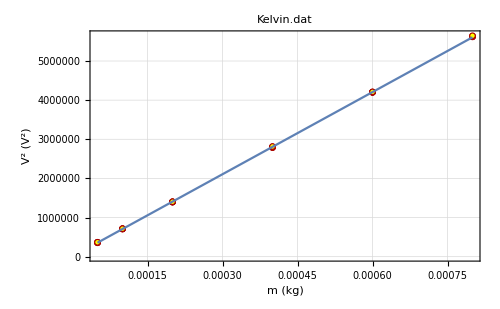
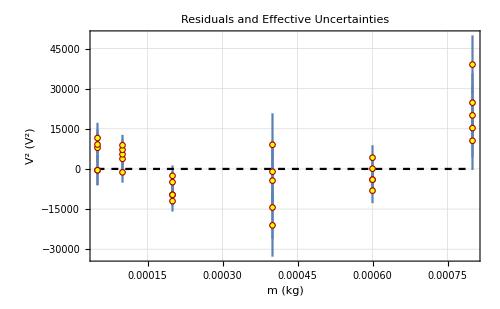
-Graphics-
-Graphics-
y(x) = a + b x
a= 
6941.72 | b= 
6.99929×10^9 | 
σ_a= 
1446.83 | σ_b= 
4.22734×10^6 | χ^2/(n-2)= 
2.828

```mathematica
LinearDifferencePlot[FrameLabel->{"m (kg)","V^2 (V^2)"}]
```

### Conclusions from fit

From the low (χ̃)^2 value (2.828) of the linear fit and the relatively small intercept (and therefore small offset), we can deduce that the V^2∝ m holds over our range of measurements. In fact, our fit determines the proportionality constant up to an error of ± 0.0604%, whereby our residuals are of the order of 10^4 but our transformed data points for V^2 have values on the order of 10^6. We therefore conclude that the data supports the proposed relationship V^2∝ m given the fit we have obtained and considering the uncertainties inherent to the system (see last section).

## Experimental determination of ϵ_0 and c

Recall the relationship V^2 = km, k = (2 gd^2)/(πr^2 ϵ_0). From this, we can find ϵ_0 from the slope k using ϵ_0 = (2 gd^2)/(πr^2 k).

We can then find the uncertainty in our value for ϵ_0 by propagating the errors:

Δϵ_0/ϵ_0 = [(Δg/g)^2+((2Δd)/d)^2+((2Δr)/r)^2+(Δk/k)^2]^(1/2). Using data from the calibration card:

```mathematica
g=9.7957;
errg=0.001;
d=0.00309;
errd=0.00005;
reff=0.03073;
errreff=0.00001;
k=6.99929*10^9;
errk=4.22733*10^6;
ϵ=(2 g d^2)/(π reff^2 k)
errϵ=ϵ*Sqrt[(errg/g)^2+(2 errd/d)^2+(2 errreff/reff)^2+(errk/k)^2]
```

9.00852×10^-12

2.91649×10^-13

We therefore have an estimate of ϵ_0 = (9.0085 ± 0.2916)×10^-12 Fm^-1. From this, we can use the permeability of free space, μ_0=4π×10^-7 Hm^-1 to estimate the speed of light in a vacuum, c.

```mathematica
μ=4 π*10^-7;
c=1/Sqrt[μ ϵ]
errc=c*errϵ/ϵ
```

2.97213×10^8

9.62222×10^6

We then estimate c = (2.9721 ± 0.0962) × 10^8 ms^-1.

## Major limiter to accuracy

Given the use of S-1 precision masses and an accurate constant-voltage power supply and careful leveling of the apparatus, it can be concluded that the major limiter to the accuracy of this experiment is the sensitivity to environmental noise inherent to the system.

In fact, by considering a parallel plate capacitor maintained under constant voltage, we observe that a small change in the distance between the plates (for instance, due to vibrations of the table due to sound or transmitted via the floor) will cause the force between the capacitor places to increase, with F/A=1/2 ϵ_0 V^2/d^2 as derived in the pre-lab. Therefore, the equilibrium point at which the force equals the weight of the mass used is an unstable equilibrium - when in the neighborhood of the equilibrium point, a small disturbance causing the top plate to move slightly past the equilibrium point will in turn cause the force between the plates to increase, accelerating the top plate downwards, which in turn increases the force between the plates and this feeds into itself until the pin stops the top plate from moving any further.

This unstable equilibrium is useful - our method of taking data points is based around it, in that moving just past the equilibrium results in the top plate moving all the way down and hitting the pin,  which is the observation that we use to take data points. However, it also introduces errors in our experiments, as small disturbances when in the neighborhood of the equilibrium point can cause the top plate to move all the way down at an incorrect voltage randomly.